```mathematica
f[k_] := 1/k;
suma =Sum[(-1)^(k-1)*f[k], {k, 1, Infinity}] (*1*)
```

Log[2]

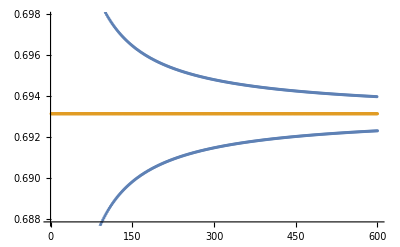

```mathematica
n = 600; (*2*)
series = Table[(-1)^(k-1)*f[k],{k,1,n}] ;
partial=Accumulate[series];
ListPlot[{partial,Table[Log[2],{i,1,n}]}]
```

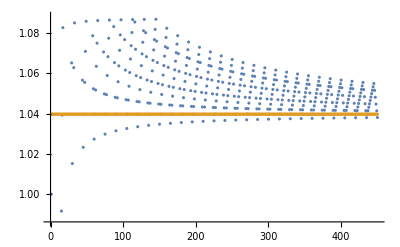

```mathematica
(*3*)
p = 10;
q = 5;
rep = 30;
ser = Table[(-1)^(k-1)*f[k], {k, 1, n}];
pos = Partition[Select[ser, (# > 0)&,  rep*p], p] ;
neg = Partition[Select[ser, (# < 0)&,  rep*q], q] ;
s =Flatten[ Table[{pos[[k]],neg[[k]]}, {k, 1, rep}]];
K =  Limit[k*f[k],k->Infinity];
Ocekavani = suma + 1/2 * K * Log[p/q];

ListPlot[{Accumulate[s], Table[Ocekavani, {x, 1, rep*(p+q)}]}]
```

```mathematica
(*4*)

(* prvni argument <g> je funkce definující alternující řadu *)
(* druhy argument <cislo> je cislo, ke kteremu chceme aby se nova rada blizila *)
(* treti <rep> urcuje pocet opakovani algoritmu *)
(* ctvrty <tol> urcuje toleranci u vysledku *)
prerovnani[g_, cislo_, rep_, tol_]:=(
suma = Sum[(-1)^(k-1)*g[k], {k, 1, Infinity}] ;
K = Limit[k*g[k],k->Infinity];
pomer = N[Exp[2*(cislo - suma)/K ]];
pomer = Rationalize[pomer, tol];
p = Numerator[pomer];
q = Denominator[pomer];

ser = Table[(-1)^(k-1)*g[k], {k, 1,2*rep* (p+q + 2)}];
pos = Partition[Select[ser, (# > 0)&,  rep*p], p] ;
neg = Partition[Select[ser, (# < 0)&,  rep*q], q] ;
s =Flatten[ Table[{pos[[k]],neg[[k]]}, {k, 1, rep}]];
ListPlot[{Accumulate[s], Table[cislo, {x, 1, rep*(p+q)}]}]
)
```

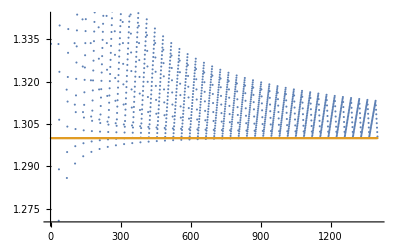

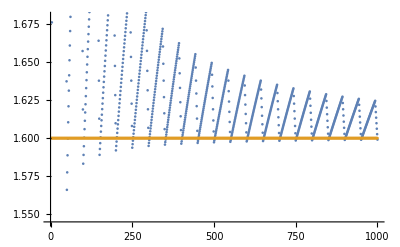

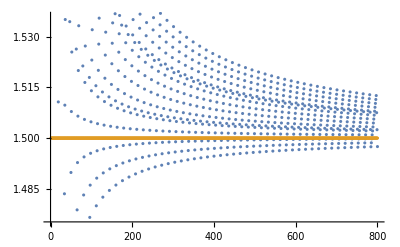

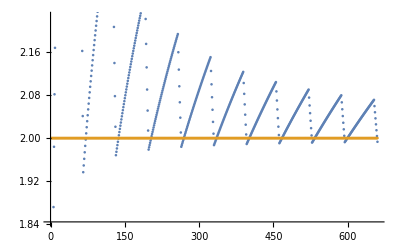

```mathematica
h[x_] := 1/x; (* zkouska 1 *)
prerovnani[h,1.3, 40, 10^(-2)]
prerovnani[h,1.6, 20, 10^(-2)]

h[x_] := (3*x+4)/(2*x^2+3*x+5); (* zkouska 2 *)
prerovnani[h,1.5, 50, 10^(-1)]
prerovnani[h,2.0, 10, 10^(-2)]
```